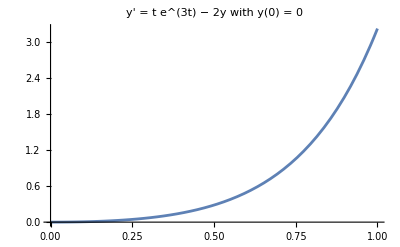

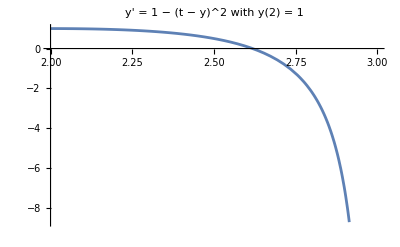

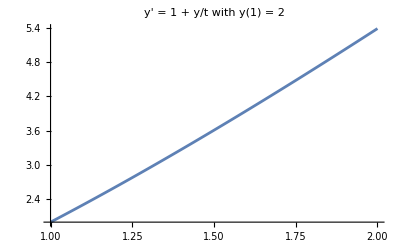

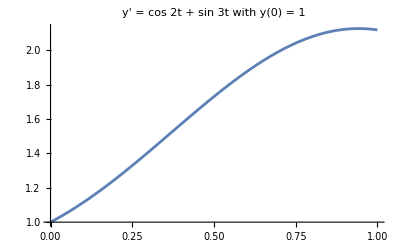

```mathematica
eq1=y'[t]==t*Exp[3*t]-2*y[t];
sol1=DSolve[{eq1,y[0]==0},y[t],t];

eq2=y'[t]==1-(t-y[t])^2;
sol2=DSolve[{eq2,y[2]==1},y[t],t];

eq3=y'[t]==1+y[t]/t;
sol3=DSolve[{eq3,y[1]==2},y[t],t];

eq4=y'[t]==Cos[2*t]+Sin[3*t];
sol4=DSolve[{eq4,y[0]==1},y[t],t];

Plot[y[t]/. sol1,{t,0,1},PlotRange->All,PlotLabel->"y' = t e^(3t) − 2y with y(0) = 0"]

Plot[y[t]/. sol2,{t,2,3},PlotRange-> Automatic,PlotLabel->"y' = 1 − (t − y)^2 with y(2) = 1"]

Plot[y[t]/. sol3,{t,1,2},PlotRange->All,PlotLabel->"y' = 1 + y/t with y(1) = 2"]

Plot[y[t]/. sol4,{t,0,1},PlotRange->All,PlotLabel->"y' = cos 2t + sin 3t with y(0) = 1"]
```